```mathematica
SetDirectory[NotebookDirectory[]]
```

H:\pedro\masters\figures\323setup\heatpipe

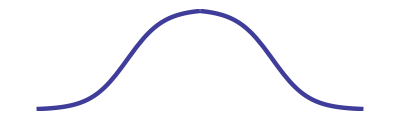

```mathematica
d=2;
l=9;
func[x_]:=Piecewise[{{Tanh[0.5 x+d],x<0},{Tanh[-(0.5 x-d)],x≥0}}]
tprofile=Plot[func[x],{x,-l,l},PlotRange->All, AspectRatio->0.3, PlotStyle->{Thickness[0.008]},Axes->False,PlotRange->All]
```

```mathematica
Export["Tprofile.svg",tprofile]
```

Tprofile.svg

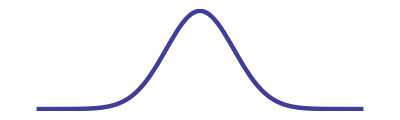

```mathematica
func[x_]:=Exp[-x^2/7]
tprofile=Plot[func[x],{x,-l,l},PlotRange->All, AspectRatio->0.3, PlotStyle->{Thickness[0.008]},Axes->False,PlotRange->All]
```

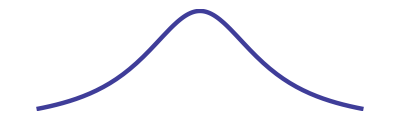

```mathematica
func[x_]:=1/(1+x^2/15)
tprofile=Plot[func[x],{x,-l,l},PlotRange->All, AspectRatio->0.3, PlotStyle->{Thickness[0.008]},Axes->False,PlotRange->All]
```

```mathematica
Export["Tprofile.svg",tprofile]
```

Tprofile.svg